# FES - Ficha 1

## Alínea A.

```mathematica
Clear[h,vc,vr,λ,deltaλ,erro,m]
(* Grandezas do Problema*)
h = 6.63*10^(-34);
λ = 18.45*10^(-10);
deltaλ = 1.4*10^(-10);
erro = 0.2*10^(-10);
m = 1.67*(10^(-27));
c= 3*10^8;
d = 10;
Nn= 150000;
```

Cálculo da velocidade dos neutrões ao longo do tubo, classica, vc, e relativista, vr:

```mathematica
vc= h/(m*λ)
vr = (h/(m*λ))/Sqrt[1+ (h/(m*λ*c))^2]
```

215.179

215.179

Cálculo do tempo que os neutrões demoram a percorrer o tubo:

```mathematica
t = d/vr
```

0.0464729

Cálculo do intervalo de tempo entre dois neutrões serem detetados no ecrã:

```mathematica
T =N[ 24*7*3600/Nn]
```

4.032

## Alínea B.

```mathematica
k = 2Pi/λ;
(* centro das fendas, no referencial esquematizado no Latex*)
x1 = 63.3*^-6;
x2 =  -62.99*^-6;
(*distância entre fendas pontuais*)
a = x1-x2;
Clear[l,r]
l=N[d/2];
(*Intensidades considerando a aproximação de FarField (ecrã longe) e sem ter em conta esta aproximação*)
Afar[xS_,l_] = Cos[a*k*xS /(2l)]^2 ;
Anear[xS_,l_] = Abs[1+Exp[I k* (Sqrt[l^2 +(xS-x1)^2 ] -Sqrt[l^2 +(xS-x2)^2 ])   ]  ]^2/4;
```

Aproximação ecrã longe:

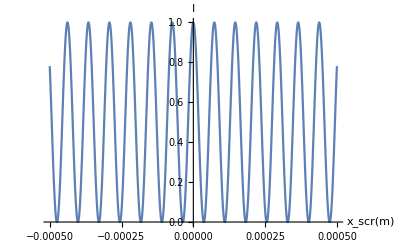

```mathematica
Plot[Afar[x,l],{x,-5*10^(-4),5*10^(-4)},AxesLabel->{HoldForm[Subscript[x,scr][m]],Ι}]
```

Distância entre Máximos:

```mathematica
N[Pi*5*2/(a*k)]
```

0.0000730462

Sem Aproximação:

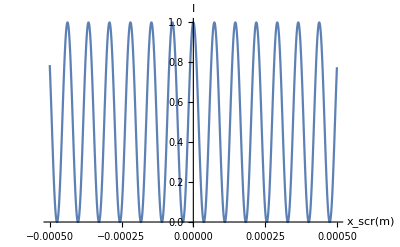

```mathematica
Plot[{Anear[x,l]},{x,-5*10^(-4),5*10^(-4)},AxesLabel->{HoldForm[Subscript[x,scr][m]],Ι}]
```

Distância entre máximos:

```mathematica
zero1=x/.FindRoot[Anear[x,l]-1,{x,0.0001}];
```

```mathematica
zero2=x/.FindRoot[Anear[x,l]-1,{x,0.}];
```

```mathematica
zero1-zero2
```

0.0000730463

## Dados Experimentais

Nas alíneas seguintes é pedido para comparar diversas simulações com os dados experimentais. Usando uma ferramenta do computador recolheram-se os seguintes pontos a partir da imagem do enunciado:

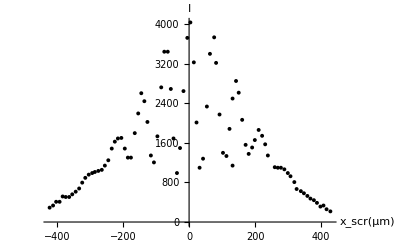

```mathematica
xsExp = {-422.81767441860467,-412.3525581395349,-403.05023255813956,-392.5851162790698,-383.28279069767444,-373.98046511627905,-363.51534883720933,-354.21302325581394,-343.74790697674416,-333.2827906976744,-323.98046511627905,-314.6781395348837,-304.21302325581394,-293.74790697674416,-285.60837209302326,-275.1432558139535,-264.6781395348837,-255.37581395348838,-244.9106976744186,-234.44558139534882,-225.1432558139535,-215.84093023255812,-205.37581395348838,-194.9106976744186,-185.60837209302323,-176.3060465116279,-164.6781395348837,-154.21302325581394,-144.9106976744186,-135.60837209302326,-126.30604651162787,-115.84093023255815,-106.53860465116276,-96.07348837209298,-84.44558139534882,-75.14325581395349,-64.67813953488371,-55.375813953488375,-47.23627906976742,-36.771162790697645,-27.468837209302308,-17.003720930232532,-5.375813953488375,3.9265116279070185,14.391627906976737,22.531162790697692,31.83348837209303,42.298604651162805,53.92651162790702,63.228837209302355,76.01953488372095,81.83348837209303,92.2986046511628,102.76372093023258,113.22883720930236,122.53116279069775,131.83348837209303,142.2986046511628,150.4381395348837,160.90325581395348,171.36837209302325,180.67069767441865,191.13581395348842,199.27534883720932,210.90325581395348,221.36837209302325,230.67069767441865,238.81023255813955,131.83348837209303,259.7404651162791,269.0427906976745,278.34511627906977,288.81023255813955,299.2753488372093,307.4148837209302,319.0427906976745,326.019534883721,338.81023255813955,348.11255813953494,358.5776744186047,367.88,378.34511627906977,387.64744186046516,398.11255813953494,407.4148837209302,416.7172093023256,428.34511627906977};
nExp ={290.3225806451613,333.3333333333333,408.6021505376344,408.6021505376344,516.1290322580645,505.37634408602145,505.37634408602145,559.1397849462365,612.9032258064516,677.4193548387096,795.6989247311827,892.4731182795698,956.9892473118279,989.2473118279569,1010.7526881720429,1032.258064516129,1053.763440860215,1139.784946236559,1247.3118279569892,1483.8709677419354,1623.6559139784945,1688.1720430107525,1698.9247311827955,1483.8709677419354,1301.0752688172042,1301.0752688172042,1795.6989247311826,2193.548387096774,2602.1505376344085,2440.860215053763,2021.5053763440858,1344.0860215053763,1204.3010752688172,1731.1827956989246,2720.4301075268813,3440.860215053763,3440.860215053763,2688.1720430107525,1688.1720430107525,989.2473118279569,1494.6236559139784,2645.1612903225805,3720.4301075268813,4032.258064516129,3225.806451612903,2010.7526881720428,1096.774193548387,1279.5698924731182,2333.333333333333,3397.849462365591,3731.1827956989246,3215.05376344086,2172.043010752688,1397.8494623655913,1333.3333333333333,1881.7204301075267,2494.6236559139784,2849.462365591398,2612.9032258064512,2064.516129032258,1559.1397849462364,1376.3440860215053,1505.3763440860214,1655.9139784946235,1860.2150537634407,1741.9354838709676,1569.8924731182794,1344.0860215053763,1139.784946236559,1107.52688172043,1096.774193548387,1096.774193548387,1064.516129032258,989.2473118279569,924.7311827956988,806.4516129032257,666.6666666666666,623.6559139784946,580.6451612903226,526.8817204301075,473.1182795698924,440.8602150537634,387.09677419354836,311.8279569892473,333.3333333333333,258.06451612903226,215.0537634408602};
expPoints = Transpose[{xsExp,nExp}];
ListPlot[expPoints,PlotStyle->Black,PlotMarkers->{Automatic,Tiny},AxesLabel->{HoldForm[Subscript[x,scr][μm]],Ι}]
```

## Alínea C.

Função que define a fenda (novo referencial):

```mathematica
f[x_] = If[x < -74, 0,
       If[x < -52.1, 1,
         If[x < 52, 0,
            If[x < 74.5, 1, 0]]]];
```

```mathematica
(*Plot[f[x], {x, -100, 100}]*)
```

k/l em μm:

```mathematica
koverL = 0.000681;
```

### Aproximação Ecrã Longe:

Transformada de Fourier : Amplitude da perturbação em pontos xscr do ecrã S4

```mathematica
ff[xscr_, kl_] = ∫_-100^100 f[x] E^Iklxscrx ⅆx;
```

Plot da Intensidade em função de xscr em S4:

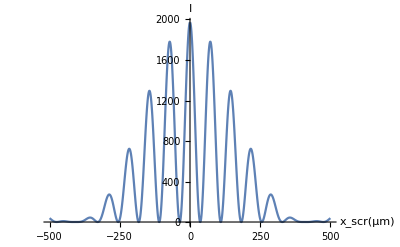

```mathematica
Plot[ff[xscr, koverL] Conjugate[ff[xscr, koverL]], {xscr, -500, 500},AxesLabel->{HoldForm[Subscript[x,scr][μm]],Ι}]
```

#### Comparação Aprox. Ecrã Longe

| Estimate | Standard Error | t-Statistic | P-Value
c1 | 2.34003 | 0.103051 | 22.7075 | 4.34917×10^-38

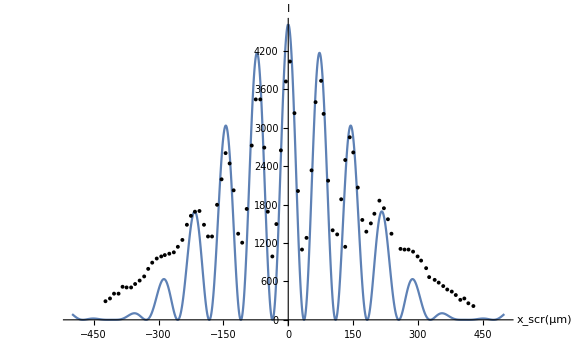

```mathematica
lm1 = NonlinearModelFit[expPoints, c1 Abs[ff[xscr, koverL]]^2,{c1},xscr];
lm1["ParameterTable"]
Show[Plot[lm1[xscr],{xscr,-500,500}],ListPlot[expPoints,PlotStyle->Black,PlotMarkers->{Automatic,Tiny}],AxesLabel->{HoldForm[Subscript[x,scr][μm]],Ι}]
```

Cálculo da Correlação

```mathematica
sum1=0;
sum2=0;
sum3=0;
For[i=1,i≤87,i++,
sum1 += nExp[[i]]* nExp[[i]];
sum2 += lm1[xsExp[[i]]]*lm1[xsExp[[i]]];
sum3 += lm1[xsExp[[i]]]* nExp[[i]];
]
CorrAproxLonge = sum3/(Sqrt[sum1*sum2])
```

0.925773

## Alínea D.

Cáculo com Expansão em Série

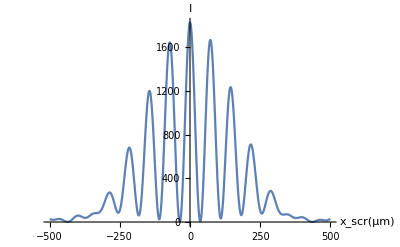

```mathematica
fdif[xscr_, kl_] = ∫_-100^100 f[x] E^(-Iklxscr(x-x^2/(2xscr)))ⅆx;
Plot[Abs[fdif[xscr,koverL]]^2,{xscr,-500,500},AxesLabel->{HoldForm[Subscript[x,scr][μm]],Ι}]
```

Cáculo Exato

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-56.4205}. NIntegrate obtained 0.441573+0.674779 ⅈ and 2.98974×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-60.2273}. NIntegrate obtained 0.576892+0.494193 ⅈ and 2.73976×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-59.6712}. NIntegrate obtained 0.648468+0.295816 ⅈ and 3.06214×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

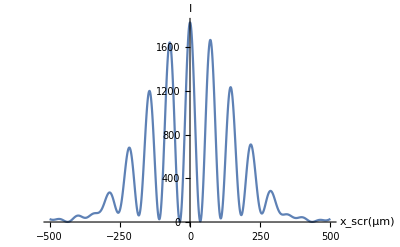

```mathematica
l=d/2*10^6;
k1 = k *10^-6;
aTot[xs_]:= Abs[NIntegrate[Exp[I k1 Sqrt[l^2 +(xs-x)^2 ]],{x,-74,-52.1}] + NIntegrate[Exp[I k1 Sqrt[l^2 +(xs-x)^2 ]],{x,52,74.5}]  ]^2;
ListLinePlot[ Transpose[{Range[-500,500,1],Map[ aTot[#]&,Range[-500,500,1] ]  }],AxesLabel->{HoldForm[Subscript[x,scr][μm]],Ι} ]
```

Sobreposição das 2 simulações com dados Experimentais

Expansão em Série:

| Estimate | Standard Error | t-Statistic | P-Value
c2 | 2.52481 | 0.0969056 | 26.0544 | 1.40873×10^-42

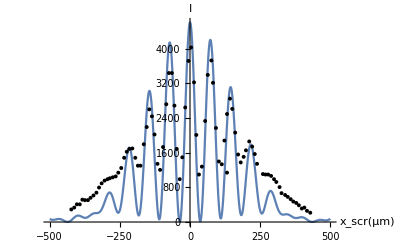

```mathematica
lm2 = NonlinearModelFit[expPoints, c2 Abs[fdif[xscr, koverL]]^2,{c2},xscr];
lm2["ParameterTable"]
Show[Plot[lm2[xscr],{xscr,-500,500}],ListPlot[expPoints,PlotStyle->Black,PlotMarkers->{Automatic,Tiny}],AxesLabel->{HoldForm[Subscript[x,scr][μm]],Ι}]
```

Cálculo da Correlação:

```mathematica
sum1=0;
sum2=0;
sum3=0;
For[i=1,i≤87,i++,
sum1 += nExp[[i]]* nExp[[i]];
sum2 += lm2[xsExp[[i]]]*lm2[xsExp[[i]]];
sum3 += lm2[xsExp[[i]]]* nExp[[i]];
]
CorrAprox2Ordem = sum3/(Sqrt[sum1*sum2])
```

0.942102

Cálculo Exato:

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-63.1787}. NIntegrate obtained 1.02273+1.96891 ⅈ and 2.61324×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-62.1093}. NIntegrate obtained -1.75165+0.422758 ⅈ and 2.85774×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-72.0755}. NIntegrate obtained 1.06738-0.00371483 ⅈ and 3.09432×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-56.4205}. NIntegrate obtained 0.441573+0.674779 ⅈ and 2.98974×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-60.2273}. NIntegrate obtained 0.576892+0.494193 ⅈ and 2.73976×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-59.6712}. NIntegrate obtained 0.648468+0.295816 ⅈ and 3.06214×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

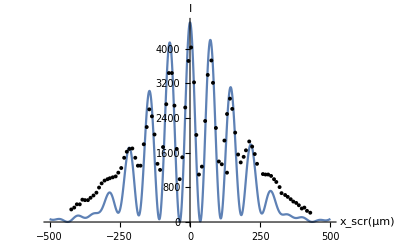

```mathematica
modelPoints = aTot[#]&@expPoints[[All,1]];
minC1=Minimize[Norm[c1 * modelPoints - expPoints[[All,2]]  ],c1];
A = c1/.minC1[[2]];

modelPlot = ListLinePlot[ Transpose[{Range[-500,500,1],Map[ A  aTot[#]&,Range[-500,500,1] ]  }]  ,PlotStyle->Default];
Show[modelPlot,ListPlot[expPoints,PlotStyle->Black,PlotMarkers->{Automatic,Tiny}],AxesLabel->{HoldForm[Subscript[x,scr][μm]],Ι}]
```

Cálculo da Correlação:

```mathematica
sum1=0;
sum2=0;
sum3=0;
For[i=1,i≤87,i++,
sum1 += nExp[[i]]* nExp[[i]];
sum2 += (c1/.minC1[[2]])*modelPoints[[i]]*(c1/.minC1[[2]])*modelPoints[[i]];
sum3 += (c1/.minC1[[2]])*modelPoints[[i]]* nExp[[i]];
]
CorrExato = sum3/(Sqrt[sum1*sum2])
```

0.942102

#### Sobreposição das Duas Simulações

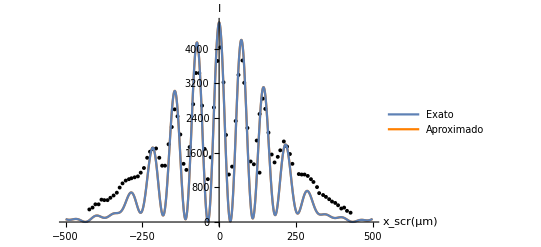

```mathematica
colors= {RGBColor[0.368417,0.506779,0.709798],Orange};
ms = {"Exato","Aproximado"};
Legended[Show[Plot[lm2[xscr],{xscr,-500,500},PlotStyle->Orange],ListPlot[expPoints,PlotStyle->Black,PlotMarkers->{Automatic,Tiny}],modelPlot,AxesLabel->{HoldForm[Subscript[x,scr][μm]],Ι}],LineLegend[colors,ms]]
```

## Alínea E.

```mathematica
lambdaM= 18.45*^-4;
lambdaS= 1.40*^-4;
```

### Distribuição Gaussiana em λ

Distribuição correspondente em k:

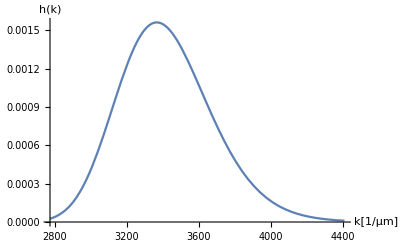

```mathematica
Plot[PDF[NormalDistribution[lambdaM ,lambdaS ],2 Pi/k ](2Pi/k^2),{k,2Pi/(lambdaM-3*lambdaS),2 Pi/(lambdaM+3*lambdaS)}, AxesLabel->{"k[1/μm]","h(k)"}]
NIntegrate[PDF[NormalDistribution[lambdaM ,lambdaS ],2 Pi/k ](2Pi/k^2),{k,2 Pi/(lambdaM+4*lambdaS),2Pi/(lambdaM-4*lambdaS)}];
```

```mathematica
packet[kl_] =PDF[NormalDistribution[lambdaM ,lambdaS ],2 Pi/kl ](2Pi/kl^2);
diffPacket[xs_]:= NIntegrate[ packet[kl] Abs[fdif[xs,kl/l]]^2 ,{kl,2 Pi/(lambdaM+4*lambdaS),2Pi/(lambdaM-4*lambdaS)}]
```

```mathematica
diffPacketPoints = Transpose[{Range[-500,500,1],Map[diffPacket[#]&,Range[-500,500,1]]    }];
```

```mathematica
modelPoints2 = diffPacket[#]&@expPoints[[All,1]];
minC2=Minimize[Norm[c2 * modelPoints2 - expPoints[[All,2]]  ]^2,c2];
```

```mathematica
diffPacketFit = MapAt[(c2/.minC2[[2]])*#&,diffPacketPoints,{All,2}];
```

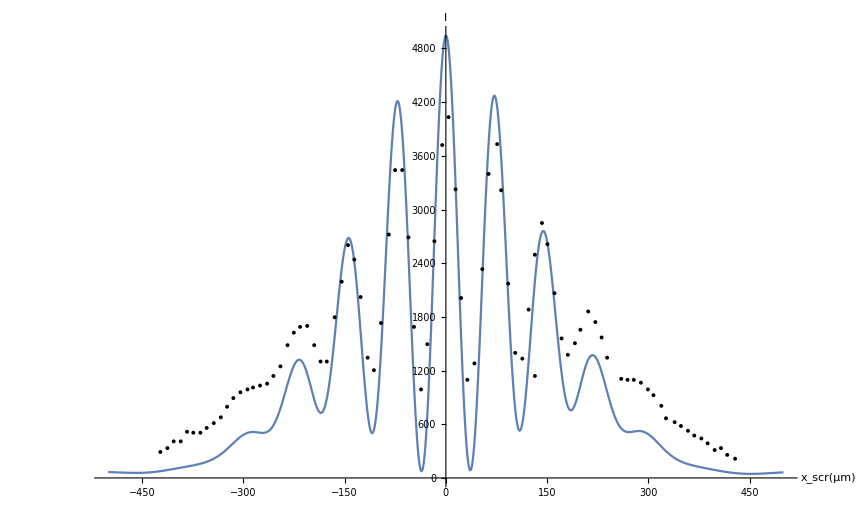

```mathematica
Show[ListLinePlot[diffPacketFit ],ListPlot[expPoints,PlotStyle->Black,PlotMarkers->{Automatic,Tiny}],AxesLabel->{HoldForm[Subscript[x,scr][μm]],Ι}]
```

Cálculo da Correlação:

```mathematica
sum1=0;
sum2=0;
sum3=0;
For[i=1,i≤87,i++,
sum1 += nExp[[i]]* nExp[[i]];
sum2 += (c2/.minC2[[2]])*modelPoints2[[i]]*(c2/.minC2[[2]])*modelPoints2[[i]];
sum3 += (c2/.minC2[[2]])*modelPoints2[[i]]* nExp[[i]];
]
CorrDistribuiçãoGauss = sum3/(Sqrt[sum1*sum2])
```

0.961489

#### Comparação com Distribuição obtida em d) [Expansão em Série]

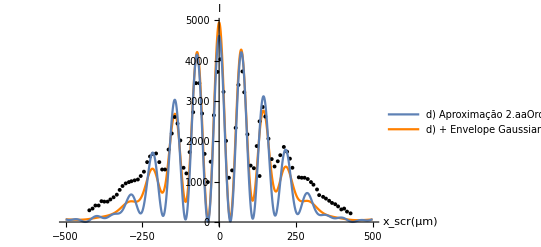

```mathematica
m2 = {"d) Aproximação 2.aaOrdem","d) + Envelope Gaussiano"};
Legended[Show[ListLinePlot[diffPacketFit ,PlotStyle->Orange],ListPlot[expPoints,PlotStyle->Black,PlotMarkers->{Automatic,Tiny}],Plot[lm2[xscr],{xscr,-500,500}],AxesLabel->{HoldForm[Subscript[x,scr][μm]],Ι}],LineLegend[colors,m2]]
```

### Distribuição Uniforme em λ

```mathematica
packetUni[kl_] =PDF[UniformDistribution[{lambdaM-lambdaS ,lambdaM+lambdaS} ],2 Pi/kl ](2Pi/kl^2);
diffPacket2[xs_]:= NIntegrate[ packetUni[kl] Abs[fdif[xs,kl/l]]^2 ,{kl,2 Pi/(lambdaM+4*lambdaS),2Pi/(lambdaM-4*lambdaS)}]
```

```mathematica
diffPacketPoints2 = Transpose[{Range[-500,500,1],Map[diffPacket2[#]&,Range[-500,500,1]] }];
```

```mathematica
modelPoints3 = diffPacket2[#]&@expPoints[[All,1]];
minC3=Minimize[Norm[c3* modelPoints3 - expPoints[[All,2]]  ]^2,c3];
```

```mathematica
diffPacketFit2 = MapAt[(c3/.minC3[[2]])*#&,diffPacketPoints2,{All,2}];
```

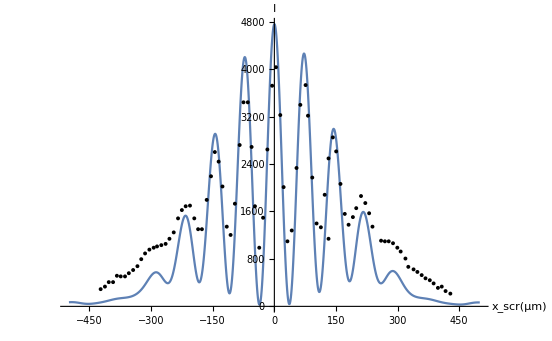

```mathematica
Show[ListLinePlot[diffPacketFit2 ],ListPlot[expPoints,PlotStyle->Black,PlotMarkers->{Automatic,Tiny}],AxesLabel->{HoldForm[Subscript[x,scr][μm]],Ι}]
```

Cálculo da Correlação:

```mathematica
sum1=0;
sum2=0;
sum3=0;
For[i=1,i≤87,i++,
sum1 += nExp[[i]]* nExp[[i]];
sum2 += (c3/.minC3[[2]])*modelPoints3[[i]]*(c3/.minC3[[2]])*modelPoints3[[i]];
sum3 += (c3/.minC3[[2]])*modelPoints3[[i]]* nExp[[i]];
]
CorrDistribuiçãoUni = sum3/(Sqrt[sum1*sum2])
```

0.951741

#### Comparação com Simulações anteriores

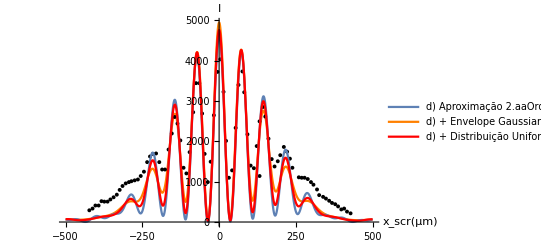

```mathematica
colors2= {RGBColor[0.368417,0.506779,0.709798],Orange,Red};
m3 = {"d) Aproximação 2.aaOrdem","d) + Envelope Gaussiano","d) + Distribuição Uniforme"};
Legended[Show[ListLinePlot[diffPacketFit ,PlotStyle->Orange],ListPlot[expPoints,PlotStyle->Black,PlotMarkers->{Automatic,Tiny}],Plot[lm2[xscr],{xscr,-500,500}],ListLinePlot[diffPacketFit2,PlotStyle->Red],AxesLabel->{HoldForm[Subscript[x,scr][μm]],Ι}],LineLegend[colors2,m3]]
```

## Alínea F.

Definição da Nova Fenda

```mathematica
g[x_] = If[x < -74.0, 0,
       If[x < -51., 1,
         If[x < 51.5, 0,
            If[x < 74.5, 1, 0]]]];
```

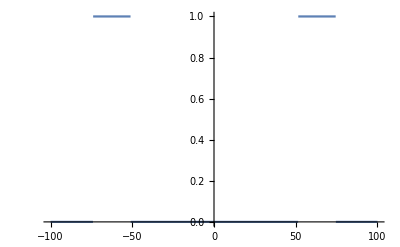

```mathematica
Plot[g[x], {x, -100, 100}]
```

```mathematica
ksobrel= (2*Pi)/(5*10^6*22.3*10^(-4))
```

0.000563514

```mathematica
ffe[xscr_, kl_] = ∫_-100^100 g[x] E^(I*kl*xscr*x)ⅆx;
```

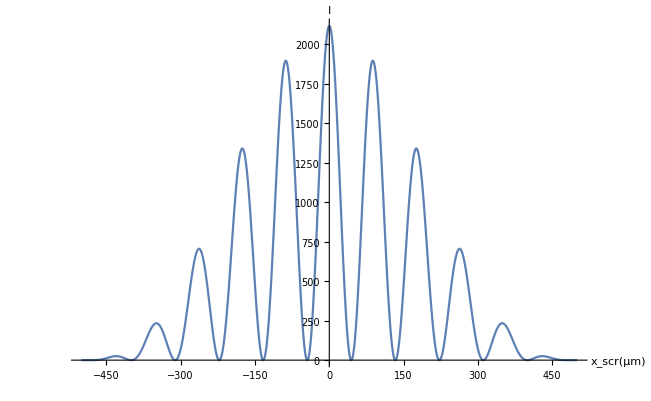

```mathematica
Plot[ffe[xscr, ksobrel] Conjugate[ffe[xscr, ksobrel]], {xscr, -500, 500},AxesLabel->{HoldForm[Subscript[x,scr][μm]],Ι}]
```

## Simulações Extra - Fenda S3

Amplitude da Perturbação em S5 devido à fenda S3:

```mathematica
Int[xs4_,kl_]= ∫_-10^10 E^(-I*kl*xs4*(x-x^2/(2xs4)))ⅆx;
```

Amplitude em S4 para um dado comprimento de onda:

```mathematica
fdif2[xscr_, kl_] = ∫_-100^100 f[x]*Int[x,kl]*E^(-Iklxscr(x-x^2/(2xscr)))ⅆx;
```

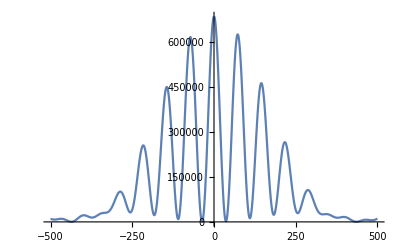

```mathematica
Plot[Abs[fdif2[xscr,koverL]]^2,{xscr,-500,500}]
```

### S3+Distribuição Gaussiana

```mathematica
diffPacket3[xs_]:= NIntegrate[ packet[kl] Abs[fdif2[xs,kl/l]]^2 ,{kl,2 Pi/(lambdaM+4*lambdaS),2Pi/(lambdaM-4*lambdaS)}]
```

```mathematica
diffPacketPoints3 = Transpose[{Range[-500,500,3],Map[diffPacket3[#]&,Range[-500,500,3]] }];
```

```mathematica
modelPoints4 = diffPacket3[#]&@expPoints[[All,1]];
minC4=Minimize[Norm[c4* modelPoints4 - expPoints[[All,2]]  ]^2,c4];
```

```mathematica
diffPacketFit3 = MapAt[(c4/.minC4[[2]])*#&,diffPacketPoints3,{All,2}];
```

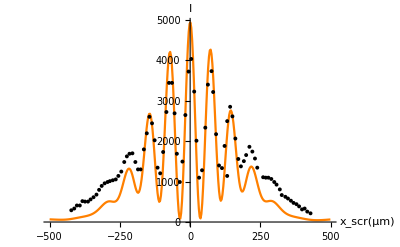

```mathematica
Show[ListLinePlot[diffPacketFit3 ,PlotStyle->Orange],ListPlot[expPoints,PlotStyle->Black,PlotMarkers->{Automatic,Tiny}],AxesLabel->{HoldForm[Subscript[x,scr][μm]],Ι}]
```

Cálculo da Correlação

```mathematica
sum1=0;
sum2=0;
sum3=0;
For[i=1,i≤87,i++,
sum1 += nExp[[i]]* nExp[[i]];
sum2 += (c4/.minC4[[2]])*modelPoints4[[i]]*(c4/.minC4[[2]])*modelPoints4[[i]];
sum3 += (c4/.minC4[[2]])*modelPoints4[[i]]* nExp[[i]];
]
CorrS3Gauss = sum3/(Sqrt[sum1*sum2])
```

0.961381

### S3+Distribuição Uniforme

```mathematica
diffPacket4[xs_]:= NIntegrate[ packetUni[kl] Abs[fdif2[xs,kl/l]]^2 ,{kl,2 Pi/(lambdaM+4*lambdaS),2Pi/(lambdaM-4*lambdaS)}]
```

```mathematica
diffPacketPoints4 = Transpose[{Range[-500,500,3],Map[diffPacket4[#]&,Range[-500,500,3]] }];
```

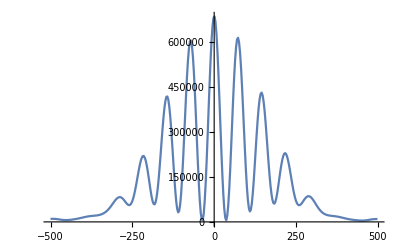

```mathematica
ListLinePlot[diffPacketPoints4]
```

```mathematica
modelPoints5 = diffPacket4[#]&@expPoints[[All,1]];
minC5=Minimize[Norm[c5* modelPoints5 - expPoints[[All,2]]  ]^2,c5];
```

```mathematica
diffPacketFit4 = MapAt[(c5/.minC5[[2]])*#&,diffPacketPoints4,{All,2}];
```

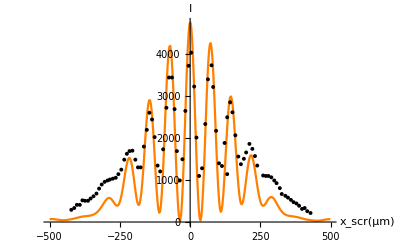

```mathematica
Show[ListLinePlot[diffPacketFit4 ,PlotStyle->Orange],ListPlot[expPoints,PlotStyle->Black,PlotMarkers->{Automatic,Tiny}],AxesLabel->{HoldForm[Subscript[x,scr][μm]],Ι}]
```

Cálculo da Correlação

```mathematica
sum1=0;
sum2=0;
sum3=0;
For[i=1,i≤87,i++,
sum1 += nExp[[i]]* nExp[[i]];
sum2 += (c5/.minC5[[2]])*modelPoints5[[i]]*(c5/.minC5[[2]])*modelPoints5[[i]];
sum3 += (c5/.minC5[[2]])*modelPoints5[[i]]* nExp[[i]];
]
CorrS3Uniforme = sum3/(Sqrt[sum1*sum2])
```

0.951661

### Sobreposição das 2 simulações:

```mathematica
colors2= {RGBColor[0.368417,0.506779,0.709798],Red,Orange,Cyan};
m4= {"d) + Envelope Gaussiano","d) + Distribuição Uniforme","d) + S3 + Envelope Gaussiano ","d) + S3 + Distribuição Uniforme"};
```

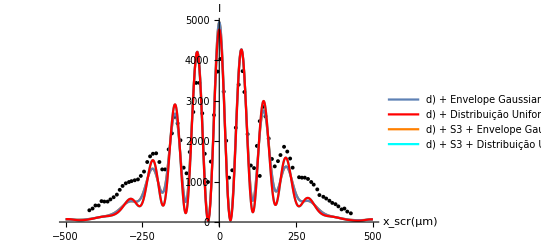

```mathematica
Legended[Show[ListLinePlot[diffPacketFit3 ,PlotStyle->Orange],ListPlot[expPoints,PlotStyle->Black,PlotMarkers->{Automatic,Tiny}],ListLinePlot[diffPacketFit4 ,PlotStyle->Cyan],ListLinePlot[diffPacketFit],ListLinePlot[diffPacketFit2,PlotStyle->Red],AxesLabel->{HoldForm[Subscript[x,scr][μm]],Ι}],LineLegend[colors2,m4]]
```

## Simulações Extra - Tamanho do detetor

```mathematica
diffPacketFit3=DeleteCases[diffPacketFit3,{_,_?(¬NumberQ[#]&)}];
```

### Tamanho do Detetor + S3 + Gaussiana

```mathematica
wD = 20;
amplitudeF = Interpolation[diffPacketFit3];
detCorr[x_] := NIntegrate[amplitudeF[t]  ,{t, x-wD/2,x+wD/2}];
```

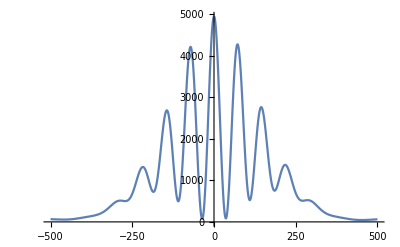

```mathematica
Plot[amplitudeF[x],{x,-500,500}]
```

```mathematica
detCorrPoints = Transpose[{Range[-500,500,1],Map[detCorr[#]&,Range[-500,500,1]]}];
```

InterpolatingFunction::dmvali: The integration endpoint -510 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint -509 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint -508 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmvali will be suppressed during this calculation.

```mathematica
modelPoints6 = Map[detCorr[#]&,expPoints[[All,1]]];
minC6=Minimize[Norm[c6 * modelPoints6 - expPoints[[All,2]]  ]^2,c6];
```

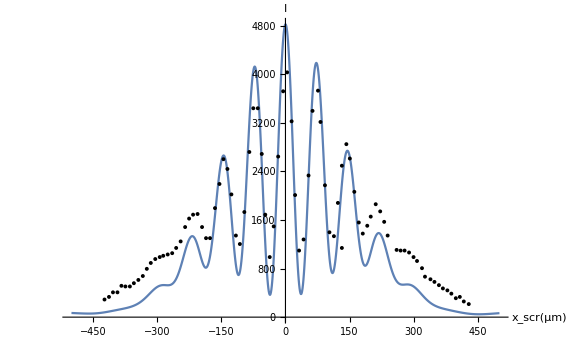

```mathematica
detCorrFit = MapAt[(c6/.minC6[[2]])*#&,detCorrPoints,{All,2}];Show[ListLinePlot[detCorrFit ,AxesLabel->{HoldForm[Subscript[x,scr][μm]],"I"}],ListPlot[expPoints,PlotStyle->Black,PlotMarkers->{Automatic,Tiny}]]
```

Cálculo Correlação:

```mathematica
sum1=0;
sum2=0;
sum3=0;
For[i=1,i≤87,i++,
sum1 += nExp[[i]]* nExp[[i]];
sum2 += (c6/.minC6[[2]])*modelPoints6[[i]]*(c6/.minC6[[2]])*modelPoints6[[i]];
sum3 += (c6/.minC6[[2]])*modelPoints6[[i]]* nExp[[i]];
]
CorrDetGauss= sum3/(Sqrt[sum1*sum2])
```

0.970487

### Tamanho Detetor + S3 + Distribuição Uniforme

```mathematica
amplitudeFU = Interpolation[diffPacketFit4];
detCorrU[x_] := NIntegrate[amplitudeFU[t]  ,{t, x-wD/2,x+wD/2}];
```

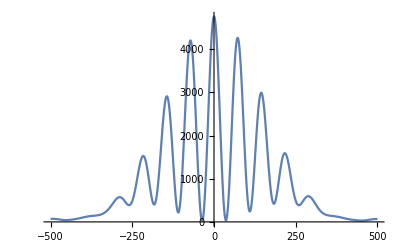

```mathematica
Plot[amplitudeFU[x],{x,-500,500}]
```

```mathematica
detCorrPointsU = Transpose[{Range[-500,500,1],Map[detCorrU[#]&,Range[-500,500,1]]}];
```

InterpolatingFunction::dmvali: The integration endpoint -510 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint -509 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint -508 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmvali will be suppressed during this calculation.

```mathematica
modelPoints7 = Map[detCorrU[#]&,expPoints[[All,1]]];
minC7=Minimize[Norm[c7 * modelPoints7- expPoints[[All,2]]  ]^2,c7];
```

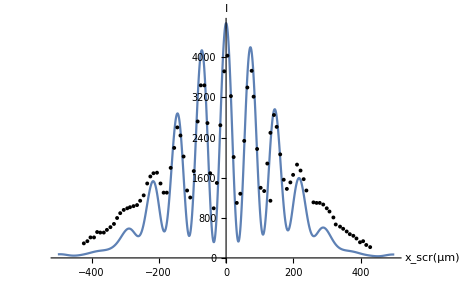

```mathematica
detCorrFitU = MapAt[(c7/.minC7[[2]])*#&,detCorrPointsU,{All,2}];Show[ListLinePlot[detCorrFitU ,AxesLabel->{HoldForm[Subscript[x,scr][μm]],"I"}],ListPlot[expPoints,PlotStyle->Black,PlotMarkers->{Automatic,Tiny}]]
```

Cálculo da Correlação:

```mathematica
sum1=0;
sum2=0;
sum3=0;
For[i=1,i≤87,i++,
sum1 += nExp[[i]]* nExp[[i]];
sum2 += (c7/.minC7[[2]])*modelPoints7[[i]]*(c7/.minC7[[2]])*modelPoints7[[i]];
sum3 += (c7/.minC7[[2]])*modelPoints7[[i]]* nExp[[i]];
]
CorrDetU= sum3/(Sqrt[sum1*sum2])
```

0.963354

### Sobreposição das 2 simulações

```mathematica
m5= {"d) + Envelope Gaussiano","d) + Distribuição Uniforme","d) + S3 + Envelope Gaussiano + Detetor ","d) + S3 + Distribuição Uniforme + Detetor"};
```

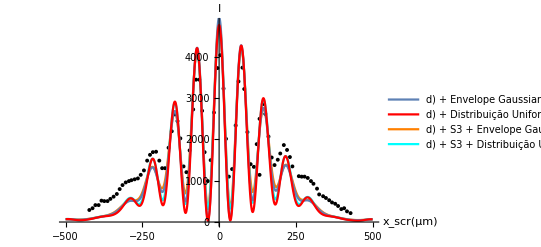

```mathematica
Legended[Show[ListLinePlot[detCorrFit ,PlotStyle->Orange],ListPlot[expPoints,PlotStyle->Black,PlotMarkers->{Automatic,Tiny}],ListLinePlot[detCorrFitU,PlotStyle->Cyan],ListLinePlot[diffPacketFit],ListLinePlot[diffPacketFit2,PlotStyle->Red],AxesLabel->{HoldForm[Subscript[x,scr][μm]],Ι}],LineLegend[colors2,m5]]
```